## Verlet

Solve the coupled system
θ' = u == f; 
u' = -θ == g;

```mathematica
f[t_,θ_,dθ_]:=dθ;
g[t_,θ_,dθ_]:=-Sin[θ];
```

```mathematica
dt=0.1; niter=200; 
t=Table[0,{i,niter}];
θ=Table[0,{i,niter}];
dθ=Table[0,{i,niter}];
```

```mathematica
verl[t0_,θ0_,dθ0_]:=Block[{t,th,dth},
th=θ0(*+0 dt f[t,θ0,dθ0]*);
dth=dθ0+dt g[t,th,dθ0]/2;
t=t0+dt/2;

th=th+dt f[t,th,dth];
dth=dth+dt g[t,th,dth]/2;
t=t+dt/2;

Return[{t,th,dth}]
]
```

```mathematica
verl[0,1,0]
```

{0.1,0.995793,-0.0840331}

```mathematica
rr=Reap[Sow[{t,θ,dθ}={0,1,0}]; Do[Sow[{t,θ,dθ}=verl[t,θ,dθ]],{i,niter}];]⟦2,1⟧;
```

```mathematica
qq[θ0_,k_,t_]:=2 ArcSin[JacobiCD[k t,Sin[θ0/2]^2] Sin[θ0/2]]
```

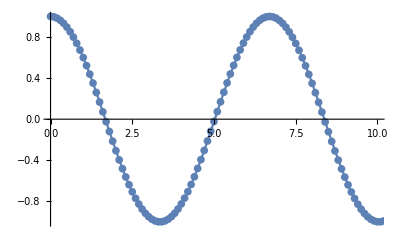

```mathematica
Show[Plot[qq[1,1,t],{t,0,10}], ListPlot[Map[{#⟦1⟧,#⟦2⟧}&,rr]]]
```

```mathematica
Mean[Map[qq[1,1,First[#]]&,rr]-Map[#⟦2⟧&,rr]]
```

-0.00036411